```mathematica
pathBase="/Users/csfloyd/Dropbox/Projects/TCB2Network/ModelDataForPaper/"; (* need to change this to where the files are located *)

r0 = 25.0;
r0String = ToString[NumberForm[r0,{5,1}]];
(* time information is in the first column of the area data *)
areaData =  Import[pathBase <>"100s/area/r0_"<>r0String<>".csv","Data"];  
times = areaData[[2;;,1]];
areas = areaData[[2;;,2]];

(* import the concentration profiles *)
BAData = Import[pathBase <>"100s/concentrations/r0_"<>r0String<>"/BA.csv","Data"]; (* first axis is time,second axis is space*)
BIData = Import[pathBase <>"100s/concentrations/r0_"<>r0String<>"/BI.csv","Data"]; 
CData = Import[pathBase <>"100s/concentrations/r0_"<>r0String<>"/C.csv","Data"]; 
DData = Import[pathBase <>"100s/concentrations/r0_"<>r0String<>"/D.csv","Data"]; 
DstData = Import[pathBase <>"100s/concentrations/r0_"<>r0String<>"/Dst.csv","Data"]; 
DAData = Import[pathBase <>"100s/concentrations/r0_"<>r0String<>"/DA.csv","Data"]; 
DIData = Import[pathBase <>"100s/concentrations/r0_"<>r0String<>"/DI.csv","Data"];
```

Time is 20. s

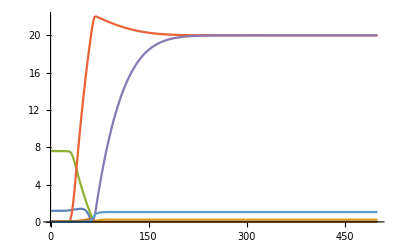

```mathematica
timeInd = 101;
Print["Time is "<>ToString[times[[timeInd]]]<>" s"];

rDomain = Range[1,500];
BAPlotData = Transpose[{rDomain,BAData[[timeInd]]}];
BIPlotData = Transpose[{rDomain,BIData[[timeInd]]}];
CPlotData = Transpose[{rDomain,CData[[timeInd]]}];
DPlotData = Transpose[{rDomain,DData[[timeInd]]}];
DstPlotData = Transpose[{rDomain,DstData[[timeInd]]}];
DAPlotData = Transpose[{rDomain,DAData[[timeInd]]}];
DIPlotData = Transpose[{rDomain,DIData[[timeInd]]}];
ListPlot[
{BAPlotData,BIPlotData,CPlotData,DPlotData,DstPlotData,DAPlotData,DIPlotData},
Joined->True,PlotRange->Full]
```

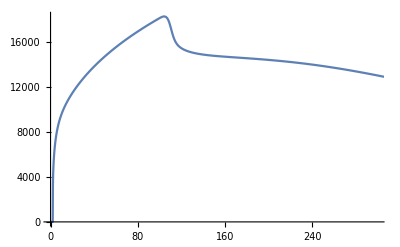

```mathematica
ListPlot[Transpose[{times,areas}],Joined->True,PlotRange->{{0,300},Automatic}]
```

```mathematica
(* start here to understand the vector plot code *)
r0String = "37.5";
vrData = Import[pathBase <>"100s/vel/r0_"<>r0String<>"/vr.csv","Data"]; (* first axis is time,second axis is space*)
```

```mathematica
t = 5 * 10; (* set the time point you want *)
rRange = Range[0,Length[vrData[[1]]]-1]; (* r values to interpolate with *)
vr = vrData[[t]]; (* get the velocity data you want *)
iFunc=Interpolation[Transpose[{rRange,vr}],InterpolationOrder->2];(* create an interpolated function *)
```

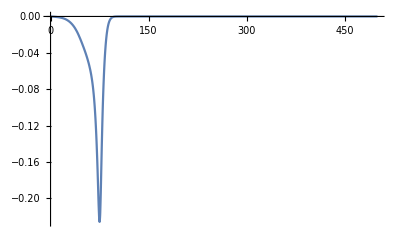

```mathematica
Plot[iFunc[r],{r,0,500},PlotRange->Full]
```

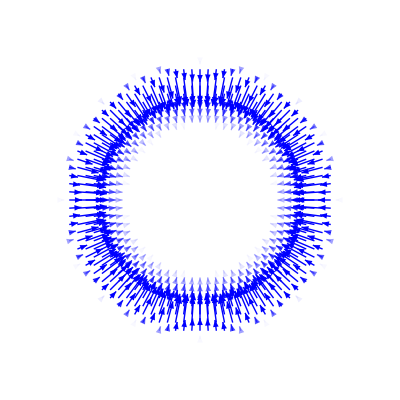

```mathematica
rFunc[x_,y_,cent_]:=Sqrt[(x-cent)^2+(y-cent)^2]
rUnit[x_,y_,cent_]:=N[{x-cent,y-cent}/(Sqrt[(x-cent)^2+(y-cent)^2]+10^-5)];


fac = 40; (* how many arrows per x range and y range do you want *)
xMax = 200;(* how big is the x range *)
yMax = xMax;(* make a square *)

lengthScale = 80; (* multiply the arrow lengths by this factor *)
opScale =40;(* controls the opacity, to use inside opacity = Log[Subscript[v, mag] * opScale]; you can change you want to control the opacity below *)
color=Blue; (* arrow color *)
ah = 0.02; (* size of the arrow heads *)
rThresh = rMax + 10; (* can uncomment this below if you don't want to draw arrows that are too far from the center *)

arrows = {};(* will be a list of Graphics objects containing arrows *)
Do[
rO= rFunc[x,y,xMax/2];(* magnitude of the vector pointing to the xy coordinate *)
rV=rUnit[x,y,xMax/2];(* unit vector pointing to the xy coordinate *)
v=iFunc[rO]; (* evaluate the interpolated function *)
p1 = {x,y};(* orign of this arrow *)
p2 = p1+lengthScale*v*rV; (* second point of the arrow *)
op = Log[Abs[v]* opScale] ;(* opacity of the arrow *)
(*If[rO<rThresh,*)
AppendTo[arrows,Graphics[{color,Opacity[op],Arrowheads[ah],Arrow[{p1,p2}]}]] (* add this arrow to the list *)
(*];*)
,{x,0,xMax,xMax/fac},{y,0,yMax,yMax/fac}];

Show[arrows]
```